```mathematica
(*SetDirectory["..."]*) (*descomentar y poner un directorio donde se guardaran los pdfs*)
Remove["Global`*"]
```

# Example 1: Discrete Exponential

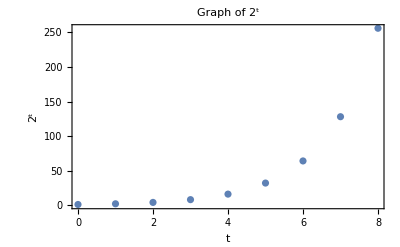

```mathematica
tValues=Range[0,8]; (*You can adjust the range as needed*)

sequenceValues=2^tValues;

PP=ListPlot[Transpose[{tValues,sequenceValues}],Mesh->All,MeshStyle->Red,Frame->True,FrameLabel->{"t",TraditionalForm[HoldForm[2^t]]
},PlotLabel->TraditionalForm[Graph of HoldForm[2^t]]]
```

```mathematica
(*Export["grafico_exponencial_discreta.pdf",PP];*) (*save as pdf*)
```

# Example 2: Continuous Exponential

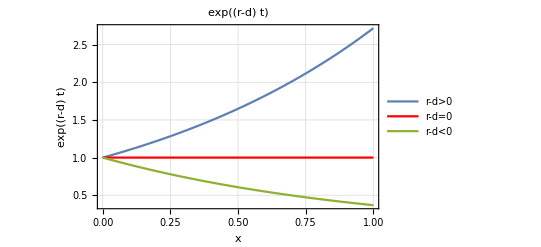

```mathematica
r=1; (*Set the value of r*)
PP=Plot[{Exp[ x],Exp[0],Exp[-x]},{x,0,1},PlotStyle->{PointSize[0.02],Red},Frame->True,FrameLabel->{"x",TraditionalForm[HoldForm[Exp[(r-d)t]]]},PlotLabel->TraditionalForm[HoldForm[Exp[(r-d)t]]],PlotLegends->{"r-d>0","r-d=0", "r-d<0"},GridLines->Automatic]
```

```mathematica
(*Export["grafico_rd.pdf",PP];*)
```

# Example 3: Logistic Equation

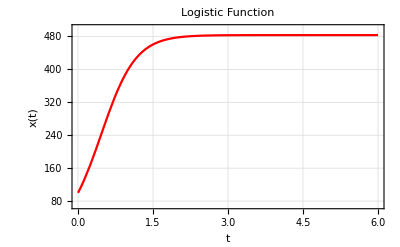

```mathematica
xt[t_,K_,r_,x0_]:=(K*x0  Exp[r t])/(K+ x0*(Exp[r t]-1))

PP2=Plot[xt[t,483.333,2.9,100],{t,0,6},PlotStyle->{PointSize[0.02],Red},Frame->True,FrameLabel->{"t","x(t)"},PlotLabel->"Logistic Function", GridLines->Automatic,PlotRange->{70,500}]
```

```mathematica
(*Export["grafico_logistic_example.pdf",PP2]*)
```

# Example 4: Differential Equation - Survival of the Fittest

Here we consider a dynamic on the simplex, where 3 species reproduce at constant rate but due to limited total abundance not all of them can survive

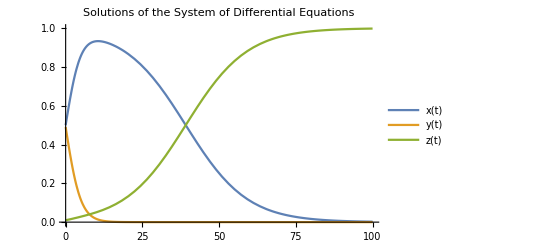

```mathematica
(*Seleccion 3 variables*)
a=1.9;b=1.5;c=2; (*fitness value*)
phi[t_]:=a*x[t]+b*y[t]+c*z[t]; (*average fitness*)
eq1=(x'[t]==(a-phi[t])*x[t]); (*the three equations*)
eq2=(y'[t]==(b-phi[t])*y[t]);
eq3=(z'[t]==(c-phi[t])*z[t]);
initialConditions={x[0]==50/100,y[0]==49/100,z[0]==1/100}; (*initial conditions*)
solution=NDSolve[{eq1,eq2,eq3,initialConditions},{x[t],y[t],z[t]},{t,0,100}]; (*function to solve the equation*)
{xSol,ySol,zSol}={x[t],y[t],z[t]}/. solution[[1]]; (*extract the solutions*)
PlotODE3=Plot[{xSol,ySol,zSol},{t,0,100},PlotLegends->{"x(t)","y(t)","z(t)"},FrameLabel->{"t","Values"},PlotLabel->"Solutions of the System of Differential Equations"] (*plot*)
```

```mathematica
(*Export["grafico_ode3var.pdf",PlotODE3]*)
```